## 163Lu

```mathematica
ClearAll["Global`*"]
```

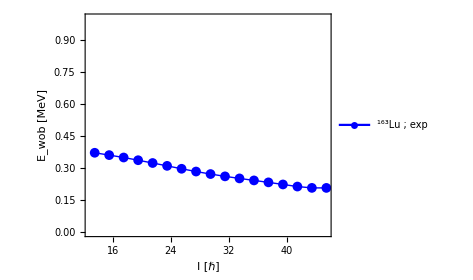

```mathematica
yrastEn=Sort[{18261,16958,15689,14461.8,13282.5,12156.2,11085.2,10068.6,9106.1,8196.4,7338.7,6533.1,5780.5,5083.5,4444.6,3865.9,3350.6,2900.3,2514.0,2199.2,1935.7,1738.9}];
wob1En=Sort[{16531,15283,14086.0,12943.0,11854.1,10819.4,9839.2,8912.7,8039.8,7219.9,6453.7,5742.5,5087.9,4492.1,3957.8,3486.2,3078.8}];
yrastSpin=Table[i/2,{i,13,97,4}];
wob1Spin=Table[i/2,{i,27,91,4}];
wobbling[yrast_,b1_,spins_]:=Table[{spins[[i]],b1[[i]]/1000-1/2(yrast[[i+3]]+yrast[[i+4]])/1000},{i,1,Length[b1]}];
data=wobbling[yrastEn,wob1En,wob1Spin];
fig=ListPlot[data,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{Thick,Blue},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black},PlotLegends->Placed[{Style[Row[{Superscript["","163"],"Lu ; exp"}],30]},{0.4,0.85}],ImageSize->350,PlotRange->{Full,{0,1}}];
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/163Lu.pdf",fig];
Show[fig]
```